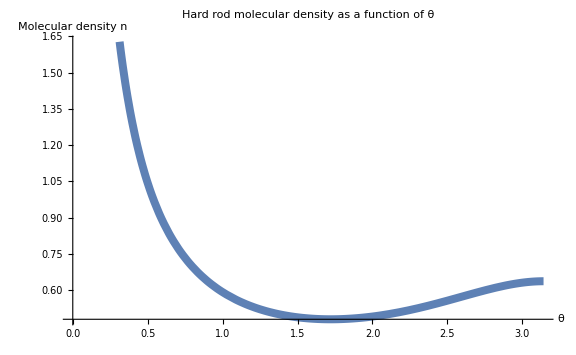

```mathematica
(* Plot of molecular density for hard rod molecules which maximizes entropy
Question 5.7c in Kardar Statistical Physics of Particles *)
f[θ_]:=2/(l^2(θ(2+Cos[θ])+Sin[θ]))
Plot[f[θ]/.l->1,{θ,0,π},PlotStyle->{Directive[Thickness[0.01]]},  AxesLabel->{Style["θ",16],Style["Molecular density n",16]},
PlotLabel->Style["Hard rod molecular density as a function of θ", Black, FontSize->20], ImageSize->Large]
```